```mathematica
Needs["MaTeX`"]
MaTeX["\\int\\frac{i x^2}{i+x^2}dx"]
pltst={{Dashing[Large]},{Dashed},{Dotted,Black},{DotDashed},Thick,Dashing[Medium]};
```

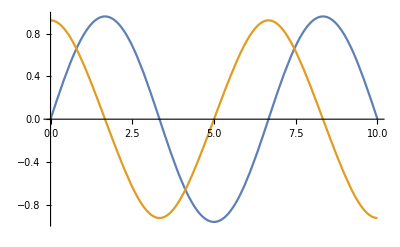
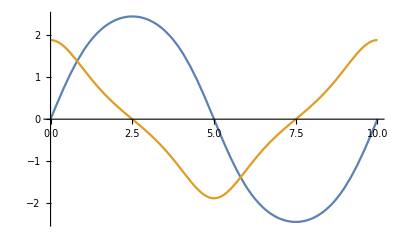
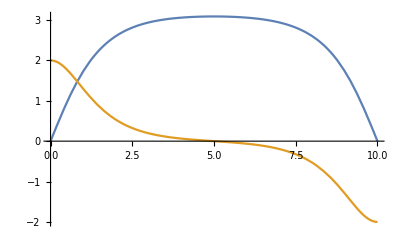
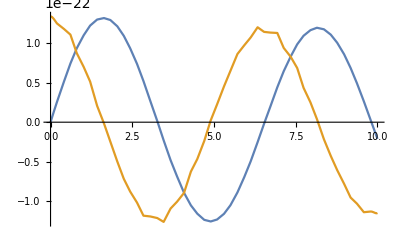

```mathematica
Table[Plot[Evaluate[{y[x], y'[x]} /. NDSolve[{y''[x] + Sin[y[x]] == 0, y[0] == 0,y[10] == 0}, y,x, Method->{"BoundaryValues"->{"Shooting", "StartingInitialConditions"->{y[0] == 0, y'[0] ==i}}}]],{x,0,10}],{i,{1.5,1.75,2,1.6}}]
```

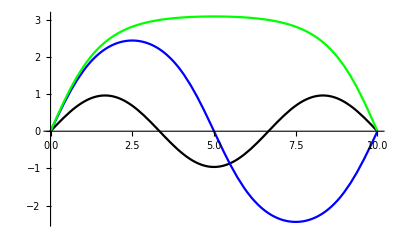

```mathematica
sols = Map[First[NDSolve[{x''[t] + Sin[x[t]] == 0, x[0] == x[10] == 0},x,t, Method->{"Shooting", "StartingInitialConditions"->{x[0] == 0, x'[0] == #}}]]&,
{1.5, 1.75, 2}];
Plot[Evaluate[x[t] /. sols], {t,0,10}, PlotStyle->{Black, Blue, Green}]
```

200

3.5

InterpolatingFunction[{{3.5, 200.}}, <>]

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {24.9891}. NIntegrate obtained 0.49181 and 0.00625938 for the integral and error estimates.

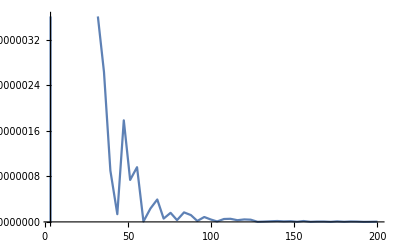

```mathematica
rf=200
ri=3.5
With[{ En=-0.0013},sol=NDSolveValue[{V0'[r]==B0[r]/r^2,B0'[r]==R2[r]^2*r^2/5.,V2'[r]==B2[r]/r^2,B2'[r]==6.*V2[r]+2.*R2[r]^2*r^2/7.,V4'[r]==B4[r]/r^2,B4'[r]==20.*V4[r]+18.*R2[r]^2*r^2/35.,R2'[r]==T[r]/r^2,T'[r]==2.*R2[r]*(3.+(V0[r]+(2./7.)*(V2[r]+V4[r])-En)*r^2),R2[ri]==0 , T[ri]==1,V0[ri]==-0.0019, V2[ri]==0, V4[ri]==0, B0[ri]==0,B2[ri]==- ri^2,B4[ri]==-ri^2},R2,{r,ri,rf},MaxStepSize->0.01]]
ar[ ri_,rf_]:=NIntegrate[x^2 sol[x]^2 ,{x,ri, rf}]
With[{A= ar[ri,rf]},Plot[sol[r]^2/A,{r,ri,rf},MaxRecursion->0,PlotPoints->50]]
```

10

3.5

InterpolatingFunction[…]

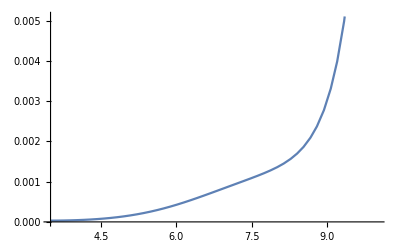

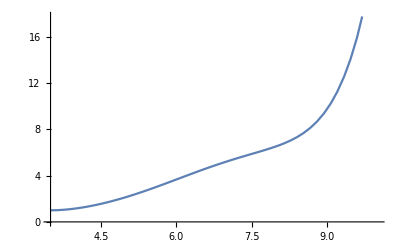

```mathematica
rf=10
ri=3.5
With[{ En=-0.0013},sol=NDSolveValue[{V0'[r]==B0[r]/r^2,B0'[r]==R2[r]^2*r^2/5.,V2'[r]==B2[r]/r^2,B2'[r]==6.*V2[r]+2.*R2[r]^2*r^2/7.,V4'[r]==B4[r]/r^2,B4'[r]==20.*V4[r]+18.*R2[r]^2*r^2/35.,R2'[r]==T[r]/r^2,T'[r]==2.*R2[r]*(3.+(V0[r]+(2./7.)*(V2[r]+V4[r])-En)*r^2),R2[ri]==0 , T[ri]==1,V0[ri]==-0.0019, V2[rf]==0, V4[rf]==0, B0[ri]==0,B2[ri]==- ri^2,B4[ri]==-ri^2},T,{r,ri,rf},MaxStepSize->0.01]]
ar[ ri_,rf_]:=NIntegrate[x^2 sol[x]^2 ,{x,ri, rf}]
With[{A= ar[ri,rf]},Plot[sol[r]^2/A,{r,ri,rf},MaxRecursion->0,PlotPoints->50]]
Plot[sol[r],{r,ri,rf},MaxRecursion->0,PlotPoints->50]
```

```mathematica
rf=10
ri=3.5
sol=NDSolveValue[{V0'[r]==B0[r]/r^2,B0'[r]==R2[r]^2*r^2/5.,V2'[r]==B2[r]/r^2,B2'[r]==6.*V2[r]+2.*R2[r]^2*r^2/7.,V4'[r]==B4[r]/r^2,B4'[r]==20.*V4[r]+18.*R2[r]^2*r^2/35.,R2'[r]==T[r]/r^2,T'[r]==2.*R2[r]*(3.+(V0[r]+(2./7.)*(V2[r]+V4[r])-En[r])*r^2),En'[r]==0,R2[ri]==0 , T[ri]==1,V0[ri]==-0.0019, V0[rf]==-0,V2[rf]==-0, V4[rf]==-0, B0[ri]==0,B2[ri]==- ri^2,B4[ri]==-ri^2},V2,{r,ri,rf},MaxStepSize->0.01]
ar[ ri_,rf_]:=NIntegrate[x^2 sol[x]^2 ,{x,ri, rf}]
With[{A= ar[ri,rf]},Plot[sol[r]^2/A,{r,ri,rf},MaxRecursion->0,PlotPoints->50]]
Plot[sol[r],{r,ri,rf},MaxRecursion->0,PlotPoints->50]
```

10

3.5

$Aborted

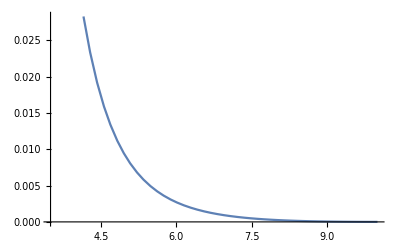

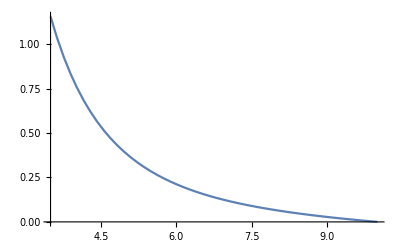

```mathematica
rf=10
ri=3.5
sol=NDSolveValue[{V0'[r]==B0[r]/r^2,B0'[r]==R2[r]^2*r^2/5.,V2'[r]==B2[r]/r^2,B2'[r]==6.*V2[r]+2.*R2[r]^2*r^2/7.,V4'[r]==B4[r]/r^2,B4'[r]==20.*V4[r]+18.*R2[r]^2*r^2/35.,R2'[r]==T[r]/r^2,T'[r]==2.*R2[r]*(3.+(V0[r]+(2./7.)*(V2[r]+V4[r])-En[r])*r^2),En'[r]==0,R2[ri]==0 , T[ri]==1,V0[ri]==-0.0019, V0[rf]==-0.1,V2[rf]==-0.1, V4[rf]==-0.1, B0[ri]==0,B2[ri]==- ri^2,B4[ri]==-ri^2},V2,{r,ri,rf},MaxStepSize->0.01]
ar[ ri_,rf_]:=NIntegrate[x^2 sol[x]^2 ,{x,ri, rf}]
With[{A= ar[ri,rf]},Plot[sol[r]^2/A,{r,ri,rf},MaxRecursion->0,PlotPoints->50]]
Plot[sol[r],{r,ri,rf},MaxRecursion->0,PlotPoints->50]
```